## Food Web Modules

### For each model below, figure out what happens along a nutrient gradient (rtot): find equilibria, their stability, and bifurcation points (where equilibria change stability) as a function of rtot. Simulate with NDSolve to verify.

## Linear Food Chain

```mathematica
μp=1;
mp=1;
μz=1;
mz=1;
μc1=1;
mc1=1;
μc2=1;
mc2=1;
Clear[rtot]
```

```mathematica
p'[t]==μp*(rtot-p[t]-z[t]-c1[t]-c2[t])*p[t]-mp*p[t]-μz*p[t]*z[t];
z'[t]==μz*p[t]*z[t]-mz*z[t]-μc1*z[t]*c1[t];
c1'[t]==μc1*z[t]*c1[t]-mc1*c1[t]-μc2*c1[t]*c2[t];c2'[t]==μc2*c1[t]*c2[t]-mc2*c2[t]
```

c2'[t]==-c2[t]+c1[t] c2[t]

```mathematica
eq=Solve[{
0==μp*(rtot-p[t]-z[t]-c1[t]-c2[t])*p[t]-mp*p[t]-μz*p[t]*z[t],
0==μz*p[t]*z[t]-mz*z[t]-μc1*z[t]*c1[t],
0==μc1*z[t]*c1[t]-mc1*c1[t]-μc2*c1[t]*c2[t],
0==μc2*c1[t]*c2[t]-mc2*c2[t]
},{p[t],z[t],c1[t],c2[t]}]
```

{{p[t]→0,z[t]→0,c1[t]→1,c2[t]→-1},{p[t]→0,z[t]→1,c1[t]→-1,c2[t]→0},{p[t]→1,z[t]→-1+rtot/2,c1[t]→0,c2[t]→0},{p[t]→2,z[t]→-1+rtot/3,c1[t]→1,c2[t]→-2+rtot/3},{p[t]→1/2 (-2+rtot),z[t]→1,c1[t]→-2+rtot/2,c2[t]→0},{p[t]→-1+rtot,z[t]→0,c1[t]→0,c2[t]→0},{p[t]→-1+rtot,z[t]→0,c1[t]→1,c2[t]→-1},{p[t]→0,z[t]→0,c1[t]→0,c2[t]→0}}

The equilibria and bifurcation points are (1, -1+rtot/2, 0, 0), (2, -1+rtot/3, 1, -2+rtot/3), (1/2(-2+rtot), 1, -2+rtot/2, 0), (-1+rtot, 0, 0, 0), and (0, 0, 0, 0).

Save plot in a variable (plot 1) for all parts, to put together, say Show[plot1, plo2....]

Here we are plotting the individual pieces of the graph:

```mathematica
Solve[(p[t]/.eq[[6]])==0,rtot]
```

{{rtot→1}}

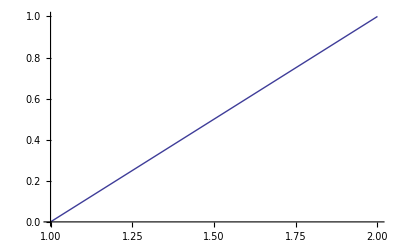

```mathematica
part1 = Plot[{p[t]/.eq[[6]]},{rtot,1,2}]
```

```mathematica
Solve[(z[t]/.eq[[3]]) ==0, rtot]
```

{{rtot→2}}

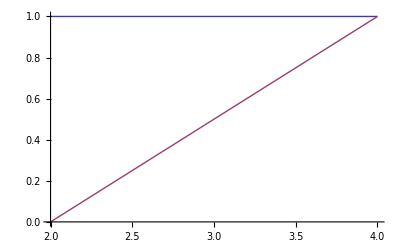

```mathematica
part2= Plot[{p[t]/.eq[[3]],z[t]/.eq[[3]]},{rtot,2,4}]
```

```mathematica
Solve[(c1[t]/.eq[[5]])==0,rtot]
```

{{rtot→4}}

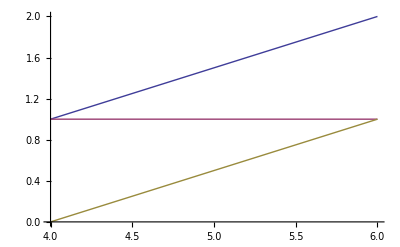

```mathematica
part3= Plot[{p[t]/.eq[[5]], z[t]/.eq[[5]], c1[t]/.eq[[5]]},{rtot,4,6}]
```

```mathematica
Solve[(c2[t]/.eq[[4]])==0,rtot]
```

{{rtot→6}}

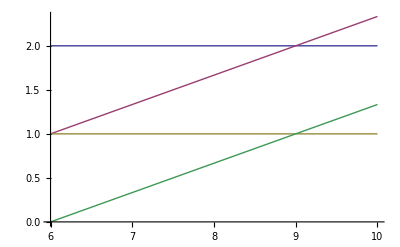

```mathematica
part4 = Plot[{p[t]/.eq[[4]],z[t]/.eq[[4]],c1[t]/.eq[[4]],c2[t]/.eq[[4]]},{rtot,6,10}]
```

And now we’ll put them all together:

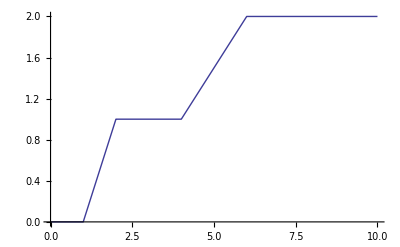

```mathematica
part1 = Plot[Piecewise[{{p[t]/.eq[[6]],1<rtot <2}, {p[t]/.eq[[3]],2<rtot<4}, {p[t]/.eq[[5]],4<rtot<6},{p[t]/.eq[[4]],6<rtot<10}}],{rtot, 0, 10}]
```

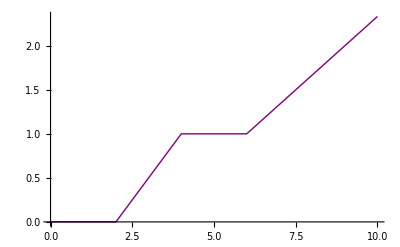

```mathematica
part2=Plot[Piecewise[{{z[t]/.eq[[3]],2<rtot<4}, {z[t]/.eq[[5]],4<rtot<6}, {z[t]/.eq[[4]],6<rtot<10}}],{rtot, 0, 10}, PlotStyle->{Purple}]
```

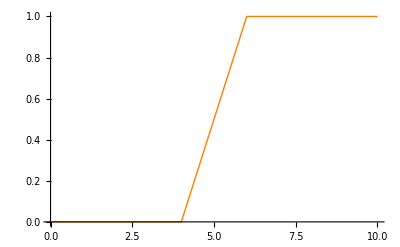

```mathematica
part3 = Plot[Piecewise[{{c1[t]/.eq[[5]],4<rtot<6},{c1[t]/.eq[[4]],6<rtot<10}}],{rtot, 0, 10}, PlotStyle->{Orange}]
```

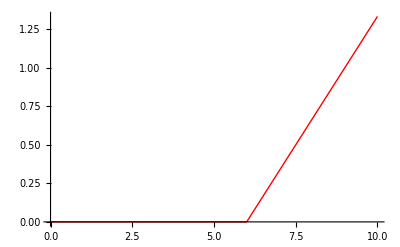

```mathematica
part4 = Plot[Piecewise[{{c2[t]/.eq[[4]],6<rtot<10}}],{rtot, 0, 10}, PlotStyle->{Red}]
```

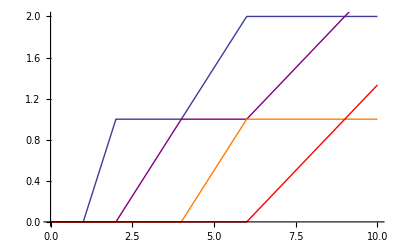

```mathematica
Show[part1, part2, part3, part4]
```

## Generalist Grazer Food Web

```mathematica
μp1=1;
μz=1;
mz=1;
μp1=1;
μp2=1;
μz2 = 1;
μz1 = 1;
y1 = 1;
y2 = 1;
yz = 1;
m1 = 1;
m2 = 1;

Clear[rtot]
```

```mathematica
p1'[t]==μp1*(rtot-p1[t]/y1-p2[t]/y2-z[t]/yz)*p1[t]-m1*p1[t]-y1/yz*μz1*p1[t]*z[t];
p2'[t]==μp2*(rtot-p1[t]/y1-p2[t]/y2-z[t]/yz)*p2[t]-m2*p2[t]-y2/yz*μz2*p2[t]*z[t];
z'[t]==μz1*p1[t]*z[t]+μz2*p2[t]*z[t]-mz*z[t]
```

z'[t]==-z[t]+p1[t] z[t]+p2[t] z[t]

```mathematica
eq=Solve[{
0==μp1*(rtot-p1[t]/y1-p2[t]/y2-z[t]/yz)*p1[t]-m1*p1[t]-y1/yz*μz1*p1[t]*z[t],
0==μp2*(rtot-p1[t]/y1-p2[t]/y2-z[t]/yz)*p2[t]-m2*p2[t]-y2/yz*μz2*p2[t]*z[t],
0==μz1*p1[t]*z[t]+μz2*p2[t]*z[t]-mz*z[t]},{p1[t],p2[t],z[t]}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{p2[t]→1-p1[t],z[t]→-1+rtot/2},{p2[t]→-1+rtot-p1[t],z[t]→0},{p1[t]→0,p2[t]→0,z[t]→0}}

```mathematica
Solve[(p2[t]/.eq[[1]])==0,rtot]
```

{}

## Specialized Grazer Food Web

```mathematica
yz1 = 1;
yz2 = 1;
yz3 = 1;
mz1 = 1;
mz2 = 1;
mz3 = 1;
μz3 = 1;
μp3 = 1;
m3 = 1;
y3 = 1;
```

```mathematica
p1'[t]==μp1*(rtot-p1[t]/y1-p2[t]/y2-p3[t]/y3-z1[t]/yz1-z2[t]/yz2-z3[t]/yz3)*p1[t]-m1*p1[t]-y1/yz1*μz1*p1[t]*z1[t];
p2'[t]==μp2*(rtot-p1[t]/y1-p2[t]/y2-p3[t]/y3-z1[t]/yz1-z2[t]/yz2-z3[t]/yz3)*p2[t]-m2*p2[t]-y2/yz2*μz2*p2[t]*z2[t];
p3'[t]==μp3*(rtot-p1[t]/y1-p2[t]/y2-p3[t]/y3-z1[t]/yz1-z2[t]/yz2-z3[t]/yz3)*p3[t]-m3*p3[t]-y3/yz3*μz3*p3[t]*z3[t];
z1'[t]==μz1*p1[t]*z1[t]-mz1*z1[t];
z2'[t]==μz2*p2[t]*z2[t]-mz2*z2[t];
z3'[t]==μz3*p3[t]*z3[t]-mz3*z3[t];
```

```mathematica
eq = Solve[{0==μp1*(rtot-p1[t]/y1-p2[t]/y2-p3[t]/y3-z1[t]/yz1-z2[t]/yz2-z3[t]/yz3)*p1[t]-m1*p1[t]-y1/yz1*μz1*p1[t]*z1[t],
0 == μp2*(rtot-p1[t]/y1-p2[t]/y2-p3[t]/y3-z1[t]/yz1-z2[t]/yz2-z3[t]/yz3)*p2[t]-m2*p2[t]-y2/yz2*μz2*p2[t]*z2[t],
0 == μp3*(rtot-p1[t]/y1-p2[t]/y2-p3[t]/y3-z1[t]/yz1-z2[t]/yz2-z3[t]/yz3)*p3[t]-m3*p3[t]-y3/yz3*μz3*p3[t]*z3[t],
0 == μz1*p1[t]*z1[t]-mz1*z1[t],
0 == μz2*p2[t]*z2[t]-mz2*z2[t],
0 == μz3*p3[t]*z3[t]-mz3*z3[t]}, {p1[t], p2[t], p3[t], z1[t], z2[t], z3[t]}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{p3[t]→-1+rtot-p1[t]-p2[t],z1[t]→0,z2[t]→0,z3[t]→0},{p1[t]→0,p3[t]→-1+rtot-p2[t],z1[t]→0,z2[t]→0,z3[t]→0},{p1[t]→1,p3[t]→-2+rtot-p2[t],z1[t]→0,z2[t]→0,z3[t]→0},{p2[t]→0,p3[t]→-1+rtot-p1[t],z1[t]→0,z2[t]→0,z3[t]→0},{p2[t]→1,p3[t]→-2+rtot-p1[t],z1[t]→0,z2[t]→0,z3[t]→0},{p2[t]→-2+rtot-p1[t],p3[t]→1,z1[t]→0,z2[t]→0,z3[t]→0},{p2[t]→-1+rtot-p1[t],p3[t]→0,z1[t]→0,z2[t]→0,z3[t]→0},{p1[t]→0,p2[t]→0,p3[t]→1,z1[t]→0,z2[t]→0,z3[t]→-1+rtot/2},{p1[t]→0,p2[t]→0,p3[t]→-1+rtot,z1[t]→0,z2[t]→0,z3[t]→0},{p1[t]→0,p2[t]→1,p3[t]→0,z1[t]→0,z2[t]→-1+rtot/2,z3[t]→0},{p1[t]→0,p2[t]→1,p3[t]→1,z1[t]→0,z2[t]→-1+rtot/3,z3[t]→-1+rtot/3},{p1[t]→0,p2[t]→1,p3[t]→-2+rtot,z1[t]→0,z2[t]→0,z3[t]→0},{p1[t]→0,p2[t]→-2+rtot,p3[t]→1,z1[t]→0,z2[t]→0,z3[t]→0},{p1[t]→0,p2[t]→-1+rtot,p3[t]→0,z1[t]→0,z2[t]→0,z3[t]→0},{p1[t]→1,p2[t]→0,p3[t]→0,z1[t]→-1+rtot/2,z2[t]→0,z3[t]→0},{p1[t]→1,p2[t]→0,p3[t]→1,z1[t]→-1+rtot/3,z2[t]→0,z3[t]→-1+rtot/3},{p1[t]→1,p2[t]→0,p3[t]→-2+rtot,z1[t]→0,z2[t]→0,z3[t]→0},{p1[t]→1,p2[t]→1,p3[t]→0,z1[t]→-1+rtot/3,z2[t]→-1+rtot/3,z3[t]→0},{p1[t]→1,p2[t]→1,p3[t]→1,z1[t]→-1+rtot/4,z2[t]→-1+rtot/4,z3[t]→-1+rtot/4},{p1[t]→1,p2[t]→1,p3[t]→-3+rtot,z1[t]→0,z2[t]→0,z3[t]→0},{p1[t]→1,p2[t]→-3+rtot,p3[t]→1,z1[t]→0,z2[t]→0,z3[t]→0},{p1[t]→1,p2[t]→-2+rtot,p3[t]→0,z1[t]→0,z2[t]→0,z3[t]→0},{p1[t]→-3+rtot,p2[t]→1,p3[t]→1,z1[t]→0,z2[t]→0,z3[t]→0},{p1[t]→-2+rtot,p2[t]→0,p3[t]→1,z1[t]→0,z2[t]→0,z3[t]→0},{p1[t]→-2+rtot,p2[t]→1,p3[t]→0,z1[t]→0,z2[t]→0,z3[t]→0},{p1[t]→-1+rtot,p2[t]→0,p3[t]→0,z1[t]→0,z2[t]→0,z3[t]→0},{p1[t]→0,p2[t]→0,p3[t]→0,z1[t]→0,z2[t]→0,z3[t]→0}}

## Bonus: Intraguild Predation

Set up a model for intraguild predation and analyze by any means possible.